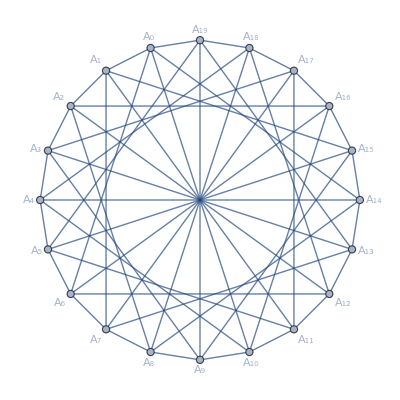

{{A_0,A_1}}

{{A_0,A_2,A_4,A_7,A_9,A_11}}

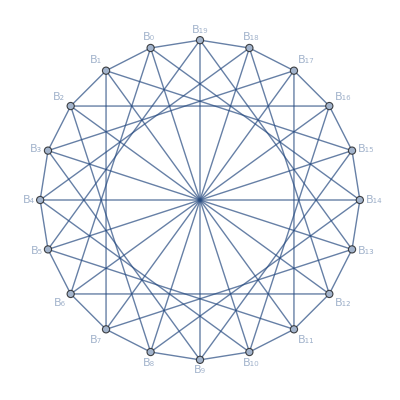

{{B_0,B_1}}

{{B_0,B_2,B_4,B_9,B_11,B_13}}

```mathematica
g1=VertexReplace[CirculantGraph[20,{1,6,10}],Table[i->Subscript[A, i-1],{i,20}]];
GraphPlot[g1,VertexLabels->"Name"]
FindClique[g1]
FindIndependentVertexSet[g1]
g2=VertexReplace[CirculantGraph[20,{1,6,10}],Table[i->Subscript[B, i-1],{i,20}]];
GraphPlot[g2,VertexLabels->"Name"]
FindClique[g2]
FindIndependentVertexSet[{g2,Subscript[B, 13]}]
(*{1,6,10} *)
```

```mathematica
g40=BooleanGraph[Or,g1,g2,VertexShapeFunction->"Name"];
Do[
edges=Flatten@Table[{Subscript[A, i]<->Subscript[B, Mod[i+k,20]],Subscript[A, i]<->Subscript[B, Mod[i+l,20]],Subscript[A, i]<->Subscript[B, Mod[i+m,20]],Subscript[A, i]<->Subscript[B, Mod[i+n,20]]},{i,0,19}];
g40plus=EdgeAdd [g40,edges];
(*(m=AdjacencyMatrix[g40]//Normal)//MatrixForm*)
If[Length@First@FindClique[g40plus]==2&&
(len=Length@First@FindIndependentVertexSet[g40plus])<=10,Print[{k,l,m,n,len}]],
{k,18},{l,k,19},{m,l,19},{n,m,19}]
```

{1,4,9,12,10}

{1,4,9,16,10}

{1,4,13,16,10}

{1,6,9,14,10}

{1,6,9,18,10}

{1,6,13,18,10}

{1,8,13,16,10}

{1,10,13,18,10}

{2,5,10,13,10}

{2,5,10,17,10}

{2,5,14,17,10}

{2,7,10,15,10}

{2,7,10,19,10}

{2,7,14,19,10}

{2,9,14,17,10}

{2,11,14,19,10}

{3,6,11,14,10}

{3,6,11,18,10}

{3,6,15,18,10}

{3,8,11,16,10}

{3,10,15,18,10}

{4,7,12,15,10}

{4,7,12,19,10}

{4,7,16,19,10}

{4,9,12,17,10}

{4,11,16,19,10}

{5,8,13,16,10}

{5,10,13,18,10}

{6,9,14,17,10}

{6,11,14,19,10}

{7,10,15,18,10}

{8,11,16,19,10}